```mathematica
Needs["CCompilerDriver`"]
```

```mathematica
mytemp1=CreateLibrary[{"/Users/dehaas/Documents/densitydependence/Cppfiles/main.cpp","/Users/dehaas/Documents/densitydependence/Cppfiles/random.cpp","/Users/dehaas/Documents/densitydependence/Cppfiles/utils.cpp"},"myLibrary","Language"->"C++","Debug"->False]
```

/Users/dehaas/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-x86-64/myLibrary.dylib

```mathematica
LibraryFunctionUnload[myFunction];
myFunction=LibraryFunctionLoad[mytemp1,"myFunction",{Integer,Integer,Real,Real,Real,Real,Integer,Integer,Integer,Integer},{Real,2}];
```

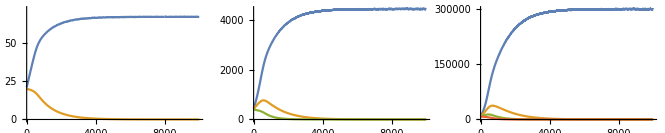

```mathematica
pars={b1->1.5,b2->0.1,d1->0.05,d2->0.05,k1->50,k2->70,tmax->10000,nrep->10000};
data=myFunction[20,20,b1/.pars,b2/.pars,d1/.pars,d2/.pars,k1/.pars,k2/.pars,tmax/.pars,nrep/.pars];
plotfirstM=ListLinePlot[{data[[;;,2]],data[[;;,3]]},PlotRange->{{0,tmax/.pars},{0,Max[k1/.pars,k2/.pars]+2}}];
plotsecondM=ListLinePlot[{data[[;;,4]],data[[;;,5]],data[[;;,6]]}];
plotthirdM= ListLinePlot[{data[[;;,7]],data[[;;,8]],data[[;;,9]],data[[;;,10]]}];
GraphicsGrid[{{plotfirstM,plotsecondM,plotthirdM}}]
```

```mathematica
(X1-EX1)(X2-EX2)(X2-EX2)//Expand
```

```mathematica
2 EX1 EX2 X2-2 EX2 X1 X2
```